# Chapter 6 Optimal Execution with Continuous Trading I

### 6.5 Liquidation with Permanent Price Impact

```mathematica
γ[ϕ_,k_]:=√(ϕ/k);
ζ[α_,b_,ϕ_,k_]:=(α-1/2 b+√(k ϕ))/(α-1/2 b-√(k ϕ));
```

```mathematica
Q[t_,T_,𝒩_,α_,b_,ϕ_/;ϕ>0,k_]:=If[α≠∞,If[ϕ≠0,𝒩(ζ[α,b,ϕ,k]Exp[γ[ϕ,k] (T-t)]-Exp[-γ[ϕ,k] (T-t)])/(ζ[α,b,ϕ,k]Exp[γ[ϕ,k] T]-Exp[-γ[ϕ,k] T]),𝒩(1-t/(T+k/α))],𝒩 Sinh[γ[ϕ,k] (T-t)]/Sinh[γ[ϕ,k] T]];
v[t_,T_,𝒩_,α_,b_,ϕ_/;ϕ>0,k_]:=If[α≠∞,γ[ϕ,k](ζ[α,b,ϕ,k]Exp[γ[ϕ,k] (T-t)]+Exp[-γ[ϕ,k](T-t)])/(ζ[α,b,ϕ,k]Exp[γ[ϕ,k] T]-Exp[-γ[ϕ,k]T])𝒩,γ[ϕ,k]𝒩 Cosh[γ[ϕ,k] (T-t)]/Cosh[γ[ϕ,k] T]];
v[t_,T_,𝒩_,α_,b_,ϕ_/;ϕ==0,k_]:=Limit[v[t,T,𝒩,α,b,i,k],i-> 0];
```

Power::infy: Infinite expression 1/0 encountered.

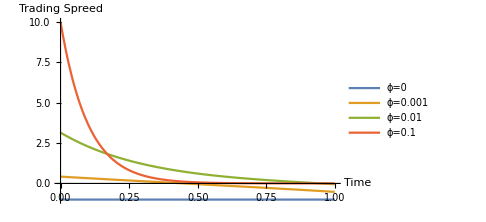
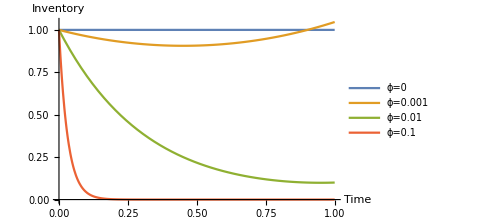
-Graphics- | -Graphics-

1.

```mathematica
With[{𝒩=1,T=1,b=10^-3,k=10^-3},
Grid[Table[{Plot[Evaluate@Table[{v[t,T,𝒩,α,b,ϕ,k]},{ϕ,{0,0.001,0.01,0.1}}],{t,0,1},PlotRange->All,
PlotLegends->Table["ϕ="<>ToString[ϕ],{ϕ,{0,0.001,0.01,0.1}}],AxesLabel->{"Time", "Trading Spreed"},ImageSize->Medium],Plot[Evaluate@Table[{Q[t,T,𝒩,α,b,ϕ,k]},{ϕ,{0,0.001,0.01,1}}],{t,0,1},
PlotLegends->Table["ϕ="<>ToString[ϕ],{ϕ,{0,0.001,0.01,0.1}}],AxesLabel->{"Time", "Inventory"},ImageSize->Medium]},{α,{0}}]]
]
```